A plot of a rotated ellipse showing the major and minor axes, and the angle of rotation.  This was related to an elliptically polarized plane wave.

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

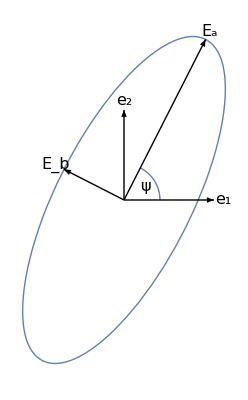

```mathematica
ClearAll[p1, bold, ellipse, fs]

bold = Style[ #, Bold] &;

ellipse[a_, b_, psi_,phi_] := Module[{e,mu,f},
e = Sqrt[1 - (b/a)^2];
mu = ArcTanh[ b/a ];
f = e a Exp[I psi] Cosh[ mu + I phi] ;
{f//Re,f//Im}
]

fs:= Style[ #, FontSize -> 16 ]&;

plotEllipse[a_, b_, psi_] :=Module[{te1, te2, e1, e2, o, va, vb, ea,eb,s},
o = {0,0};
va = ellipse[a,b,psi,0];
vb = ellipse[a,b,psi,Pi/2];
s = 0.1;
{e1,e2} = IdentityMatrix[2];
te1 = Subscript["e"// bold , 1]//fs;
te2 = Subscript["e"// bold, 2]//fs;
ea = Subscript["E"// bold, "a"]//fs;
eb = Subscript["E"// bold, "b"]//fs;
Show[{
ParametricPlot[
ellipse[a,b,psi, t],{t,0,2 Pi},
Ticks  -> None,
PlotStyle-> Thick,
Axes -> None
],
ParametricPlot[(a/5){Cos[t],Sin[t]},{t,0,psi}, PlotStyle-> Thick],
Graphics[{
Thick,
Arrow[{o, e1}],
Arrow[{o, e2}],
Text[te1, (1+s) e1],
Text[te2, (1+s) e2],
Arrow[{o,va}],
Arrow[{o,vb}],
Text[ea, va + s(va//Normalize)],
Text[eb, vb + s(vb//Normalize)],
Text[ "ψ"//fs, ellipse[a,b,psi/2,0]/7]
}
,AspectRatio-> 1
]
}]
];

p1 = plotEllipse[2,.75,0.35 Pi] 
(*p2 = plotEllipse[3,0,0.35 Pi] *)
```

```mathematica
peeters`exportForLatex["ellipticalPolarizationFig1", p1]
```

{ellipticalPolarizationFig1.eps,ellipticalPolarizationFig1pn.png}

```mathematica
Manipulate[
plotEllipse[a,b,psi] 
,{{a,3, "E_a"},1,100}
,{{b,1.5, "E_b"},0,0.99 a}
, {{psi,0.35 Pi, "ψ"},0, 2Pi}
]
```